```mathematica
f[a1_,x_,y_]=x-x*y/(1+a1*x)-0.01*x*x;
```

```mathematica
g[a1_,d0_,x_,y_]=-y+x*y/(1+a1*x)-d0*y*y;
```

```mathematica
funcr[a1_, d0_, x_] = -1-a1*x+x-d0*(1+2*a1*x+(a1^2)*x^2-0.01*x-0.02*a1*x^2-0.01*(a1^2)*x^3)
```

-1+x-a1 x-d0 (1-0.01 x+2 a1 x-0.02 a1 x^2+a1^2 x^2-0.01 a1^2 x^3)

```mathematica
Solve[{funcr[0.4,0.23,x]==0},x]
```

{{x→4.68298},{x→8.75029},{x→81.5667}}

```mathematica
equlibr[d0_]=Solve[{funcr[0.4,d0,x]==0},x]
```

{{x→31.6667+((131.242-227.317 ⅈ) (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0},{x→31.6667+((131.242+227.317 ⅈ) (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((82.6771-143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0},{x→31.6667-(262.484 (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+(165.354 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0}}

```mathematica
Eq1X[d0_]=x//.equlibr[d0][[1]]
```

31.6667+((131.242-227.317 ⅈ) (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0

```mathematica
Eq2X[d0_]=x//.equlibr[d0][[2]]
```

31.6667+((131.242+227.317 ⅈ) (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((82.6771-143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0

```mathematica
Eq3X[d0_]=x//.equlibr[d0][[3]]
```

31.6667-(262.484 (0.00288 d0-0.026896 d0^2))/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+(165.354 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0

```mathematica
EqY[d0_,x_]= ((x/(1+0.4*x))-1)/d0
```

(-1+x/(1+0.4 x))/d0

```mathematica
Eq1X[0.23]
Eq2X[0.23]
Eq3X[0.23]
```

8.75029-1.77636×10^-14 ⅈ

4.68298+1.06581×10^-14 ⅈ

81.5667+6.66134×10^-16 ⅈ

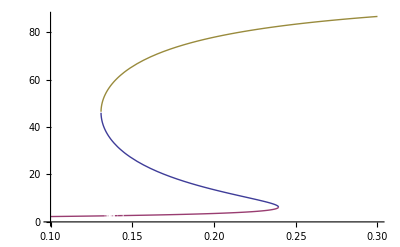

```mathematica
Plot[{Eq1X[d0],Eq2X[d0],Eq3X[d0]},{d0,0.1,0.3}]
```

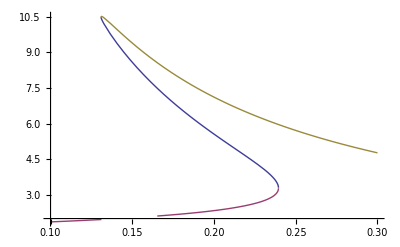

```mathematica
Plot[{EqY[d0,Eq1X[d0]], EqY[d0,Eq2X[d0]], EqY[d0,Eq3X[d0]]}, {d0, 0.1, 0.3}]
```

```mathematica
Export["C:\\1.eps",%]
```

Export::noopen: Cannot open "C:\\1.eps".

$Failed

```mathematica
fx[a1_,x_,y_]=D[f[a1,x,y],x];
```

```mathematica
fy[a1_,x_,y_]=D[f[a1,x,y],y];
```

```mathematica
gx[a1_,d0_,x_,y_]=D[g[a1,d0,x,y],x];
```

```mathematica
gy[a1_,d0_,x_,y_]=D[g[a1,d0,x,y],y];
```

```mathematica
det[a1_,d0_,x_,y_,lam_]=(fx[a1,x,y]-lam)*(gy[a1,d0,x,y]-lam)-fy[a1,x,y]*gx[a1,d0,x,y];
```

```mathematica
det1[d0_, x_, y_, lam_] = det[0.4,d0,x,y,lam];
```

```mathematica
re=Solve[{det1[d0, Eq1X[d0], EqY[d0, Eq1X[d0]], lam]==0},lam]
```

{{lam→0.5 (1.36667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-«22» «1»+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((«22» «1» √(«1») d0^(3/2)-«1»+«1»)^(1/3))+«27»+((«19»-«18» ⅈ) d0)/((«1»)^(1/3) («1»))+((82.6771+143.201 ⅈ) («1»)^(1/3))/(d0 (13.6667+(0.151191-«19» ⅈ)/(«1»)^(1/3)-((«19»-«1») d0)/(«1»)^(1/3)-((33.0709+57.2804 ⅈ) («1»)^(1/3))/d0))-1. √((-1.36667+«31»)^2-4. (0.366667-(0.00755953-0.0130935 ⅈ)/(«1»)^(1/3)+(«1»)/(«1»)^(«1»)+«60»)))},{lam→0.5 («1»)}}

```mathematica
lam1[d0_] = lam/.re[[1]]
```

0.5 (1.36667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)+1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-1. √(((-1.36667+(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0+(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))))^2-4. (0.366667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-((6315.44-4.06544×10^-13 ⅈ) √(-0.239456+d0) √(-0.130881+d0))/(d0^(5/2) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(23500.+1.06983×10^-12 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(234750.+8.82203×10^-12 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(9.68256+1.33227×10^-15 ⅈ)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(0.3456+5.55112×10^-17 ⅈ)/(d0 (-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((90.4244+1.42109×10^-14 ⅈ) d0)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((281.488+4.26326×10^-14 ⅈ) d0^2)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(405.6+702.52 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(21.7156+37.6126 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1893.93+3280.38 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(18384.8-31843.4 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(113.393-196.402 ⅈ)/(d0^2 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(3027.59-5243.94 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((24803.1+42960.3 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((430610.+745839. ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1.039×10^6-1.7996×10^6 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(800.+3.55271×10^-14 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(10680.+5.11591×10^-13 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(17.0779+29.5798 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.914343+1.58369 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((79.7443+138.121 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(715.389-1239.09 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(76.6032-132.681 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((16755.9+29022.1 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((43747.3-75772.5 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-107.667/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(12.0016-20.7874 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(1.28512-2.22589 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((281.102+486.883 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(35.0833+0. ⅈ)/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-(4.+2.22045×10^-16 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.00571464+0.00989805 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((0.106737+0.184874 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.498402+0.863257 ⅈ) d0^2)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.100794-0.17458 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.941301-1.63038 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((22.0472+38.1869 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((273.42-473.578 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)))))

```mathematica
lam2[d0_]=lam/.re[[2]]
```

0.5 (1.36667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)+1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+√(((-1.36667+(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0+(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))))^2-4. (0.366667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-((6315.44-4.06544×10^-13 ⅈ) √(-0.239456+d0) √(-0.130881+d0))/(d0^(5/2) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(23500.+1.06983×10^-12 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(234750.+8.82203×10^-12 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(9.68256+1.33227×10^-15 ⅈ)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(0.3456+5.55112×10^-17 ⅈ)/(d0 (-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((90.4244+1.42109×10^-14 ⅈ) d0)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((281.488+4.26326×10^-14 ⅈ) d0^2)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(405.6+702.52 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(21.7156+37.6126 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1893.93+3280.38 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(18384.8-31843.4 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(113.393-196.402 ⅈ)/(d0^2 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(3027.59-5243.94 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((24803.1+42960.3 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((430610.+745839. ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1.039×10^6-1.7996×10^6 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(800.+3.55271×10^-14 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(10680.+5.11591×10^-13 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(17.0779+29.5798 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.914343+1.58369 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((79.7443+138.121 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(715.389-1239.09 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(76.6032-132.681 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((16755.9+29022.1 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((43747.3-75772.5 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-107.667/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(12.0016-20.7874 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(1.28512-2.22589 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((281.102+486.883 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(35.0833+0. ⅈ)/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-(4.+2.22045×10^-16 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.00571464+0.00989805 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((0.106737+0.184874 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.498402+0.863257 ⅈ) d0^2)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.100794-0.17458 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.941301-1.63038 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((22.0472+38.1869 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((273.42-473.578 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)))))

```mathematica
lam[d0_]=Re[lam2[d0]]
```

0.5 (1.36667+Re[-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)+1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+√(((-1.36667+(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0+(100.+7.10543×10^-15 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(1335.+5.68434×10^-14 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(2.13474+3.69747 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(0.114293+0.197961 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((9.96804+17.2651 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(89.4236-154.886 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(9.5754-16.5851 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((2094.49+3627.76 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+((5468.41-9471.56 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+44.3333/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(4.94183-8.5595 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(0.529167-0.916544 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-((115.748+200.481 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+31.6667/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-1./(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.377976-0.654674 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((3.52988-6.11393 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((82.6771+143.201 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))))^2-4. (0.366667-(0.00755953-0.0130935 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((0.0705976-0.122279 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))+((1.65354+2.86402 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0-((6315.44-4.06544×10^-13 ⅈ) √(-0.239456+d0) √(-0.130881+d0))/(d0^(5/2) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(23500.+1.06983×10^-12 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(234750.+8.82203×10^-12 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(9.68256+1.33227×10^-15 ⅈ)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(0.3456+5.55112×10^-17 ⅈ)/(d0 (-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((90.4244+1.42109×10^-14 ⅈ) d0)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((281.488+4.26326×10^-14 ⅈ) d0^2)/((-0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)+0.00124416 d0^2-0.00882189 d0^3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(405.6+702.52 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(21.7156+37.6126 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1893.93+3280.38 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(18384.8-31843.4 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+(113.393-196.402 ⅈ)/(d0^2 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(3027.59-5243.94 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-((24803.1+42960.3 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((430610.+745839. ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)+((1.039×10^6-1.7996×10^6 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^4)-(800.+3.55271×10^-14 ⅈ)/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(10680.+5.11591×10^-13 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(17.0779+29.5798 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(0.914343+1.58369 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((79.7443+138.121 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-(715.389-1239.09 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)+(76.6032-132.681 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((16755.9+29022.1 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-((43747.3-75772.5 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^3 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^3)-107.667/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(12.0016-20.7874 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)-(1.28512-2.22589 ⅈ)/(d0 (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+((281.102+486.883 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)^2)+(35.0833+0. ⅈ)/(13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0)-(4.+2.22045×10^-16 ⅈ)/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-(0.00571464+0.00989805 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+((0.106737+0.184874 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.498402+0.863257 ⅈ) d0^2)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))+(0.100794-0.17458 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((0.941301-1.63038 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3) (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((22.0472+38.1869 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/(d0 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))-((273.42-473.578 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(2/3))/(d0^2 (13.6667+(0.151191-0.26187 ⅈ)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((1.41195-2.44557 ⅈ) d0)/((0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))-((33.0709+57.2804 ⅈ) (0.00174609 √(-0.239456+d0) √(-0.130881+d0) d0^(3/2)-0.00124416 d0^2+0.00882189 d0^3)^(1/3))/d0))))])

```mathematica
Plot[{lam[d0],lam1[d0],lam2[d0]},{d0,0.1,0.3}]
```

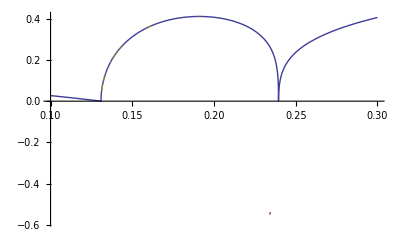

```mathematica
Export["C://1.png", %]
```

Export::noopen: Cannot open "C://1.png".

$Failed

{{1,2},{-1,2}}

$Failed

{{1,2},{-1,2}}

{{1,2},{-1,2}}

```mathematica
S={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
MatrixForm[W={{2*a1,4},{1,3}}]
```

(2 a1 | 4
1 | 3)

```mathematica
R=F.W+W.Transpose[F]
```

{{10+4 a1,18-2 a1},{9-2 a1,7}}

```mathematica
Solve[{10+4 a1==-1,18-2 a1==0,9-2 a1==0,a1==-1},{w1,w2,w3,w4}]
```

{}

```mathematica
R
```

{{10+4 a1,18-2 a1},{9-2 a1,7}}

General::ivar: {1, 3} is not a valid variable.

Solve[False,{{2 a1,4},{1,3}}]

```mathematica
MatrixForm[R]
```

(10+4 a1 | 18-2 a1
9-2 a1 | 7)

```mathematica
Eigenvalues[R]
```

{1/2 (17+4 a1-√(657-192 a1+32 a1^2)),1/2 (17+4 a1+√(657-192 a1+32 a1^2))}

```mathematica
Eigenvectors[R]
```

{{-(3+4 a1-√(657-192 a1+32 a1^2))/(2 (-9+2 a1)),1},{-(3+4 a1+√(657-192 a1+32 a1^2))/(2 (-9+2 a1)),1}}

```mathematica
Clear[L1Mass]
L1Mass=Array[hg,{3,1200}];
For[ a1=0.601;l=0,a1<1.8,a1=a1+0.001;l++{L1Mass[[1,l]]=a1,L1Mass[[2,l]]=lam1[a1],L1Mass[[3,l]]=lam2[a1]}]
```

```mathematica
Clear[L2Mass]
L2Mass=Array[hg,{2,1801}];
For[ a1=0;l=0,a1<1.8,a1=a1+0.001;l++{L2Mass[[1,l]]=a1,L2Mass[[2,l]]=1/2 (17+4 a1-√(657-192 a1+32 a1^2))}]
```

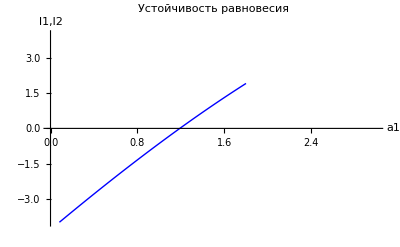

```mathematica
ListPlot[Transpose[L2Mass],PlotStyle->{{Blue,PointSize[Large]}},AxesLabel->{Style["a1",Large],Style["l1,l2",Large]},Joined->True,PlotRange->{{0,3},{-4,4}},PlotLabel->Style[Framed["Устойчивость равновесия"],16]]
```

```mathematica
Export["C:\\Таня\\ПМП\\a1.txt",L2Mass[[1]], "List"]
```

C:\Таня\ПМП\a1.txt

```mathematica
Export["C:\\Таня\\ПМП\\m1.txt",L2Mass[[2]],"List"]
```

C:\Таня\ПМП\m1.txt